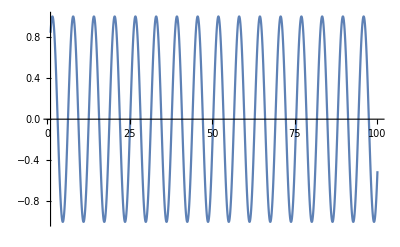
{{-Graphics-},{□},{□}}

```mathematica
{{Plot[Sin[x],{x,1,100}]}, {□}, {□}}
```

```mathematica
Transpose[%1]
```

{{-Graphics-,□,□}}

```mathematica
Dimensions[%2]
```

{1,3}

```mathematica
Total[{1,3}]
```

4

```mathematica
Range[4]
```

{1,2,3,4}

```mathematica
Partition[{1,2,3,4},6]
```

{}

```mathematica
Code
```

```mathematica
data={{Import["L:\promec\Animesh\MK\proteinGroups.txt","Table"]}, {□}}//Shallow
```

{{{«4508»}},{□}}

```mathematica
data=SemanticImport["L:\promec\Animesh\MK\proteinGroups.txt",Delimiters->"\t",HeaderLines->1]
```

Dataset[<>]

```mathematica
Dimensions[data]
```

{4507,276}

```mathematica
data[All,"Intensity"]
Histogram[Log2[data[All,"Intensity"]]//Normal]
```

Dataset[<>]

Histogram::ldata: Log[Dataset[«4507»]]/Log[2] is not a valid dataset or list of datasets.

Histogram[1/Log[2]Log[Dataset[<>]]]

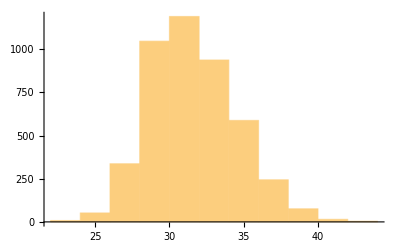

```mathematica
Histogram[data[All,"Intensity",Log2]]
```

```mathematica
dist=FindDistribution[intensity=Normal@data[All,"Intensity"]]

dist=FindDistribution[data[All,"Intensity",Log2]//Normal]
```

FindDistribution::conenf: The data will be treated as continuous. Use the option TargetFunctions->Discrete otherwise.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

Pick::incomp: Expressions {NormalDistribution[2.32805×10^10,3.5×10^6],HalfNormalDistribution[5.38354×10^-11],UniformDistribution[{2.3277×10^10,2.3284×10^10}],LogNormalDistribution[23.8709,0.00015034],InverseGaussianDistribution[2.32805×10^10,1.03001×10^18],ChiSquareDistribution[2.32805×10^10],«4»,LaplaceDistribution[2.32805×10^10,3.5×10^6],LogisticDistribution[2.32805×10^10,2.22817×10^6],MaxwellDistribution[1.3441×10^10],ExtremeValueDistribution[2.32787×10^10,3.15111×10^6],DataDistribution[Histogram,{{1.×10^-7,1.×10^-7},{2.3275×10^10,2.328×10^10,2.3285×10^10}},1,4],ExponentialDistribution[4.29544×10^-11]} and {Indeterminate≥1/16,Indeterminate≥1/16,Indeterminate≥1/16,Indeterminate≥1/16,Indeterminate≥1/16,Indeterminate≥1/16,Indeterminate≥1/16,Indeterminate≥1/16,False,Indeterminate≥1/16,Indeterminate≥1/16,Indeterminate≥1/16,Indeterminate≥1/16,Indeterminate≥1/16,Indeterminate≥1/16,Indeterminate≥1/16} have incompatible shapes.

Join::heads: Heads List and Pick at positions 1 and 2 are expected to be the same.

Join::heads: Heads List and Pick at positions 1 and 3 are expected to be the same.

Pick::incomp: Expressions {NormalDistribution[2.32805×10^10,3.5×10^6],HalfNormalDistribution[5.38354×10^-11],UniformDistribution[{2.3277×10^10,2.3284×10^10}],LogNormalDistribution[23.8709,0.00015034],InverseGaussianDistribution[2.32805×10^10,1.03001×10^18],ChiSquareDistribution[2.32805×10^10],«4»,LaplaceDistribution[2.32805×10^10,3.5×10^6],LogisticDistribution[2.32805×10^10,2.22817×10^6],MaxwellDistribution[1.3441×10^10],ExtremeValueDistribution[2.32787×10^10,3.15111×10^6],DataDistribution[Histogram,{{1.×10^-7,1.×10^-7},{2.3275×10^10,2.328×10^10,2.3285×10^10}},1,4],ExponentialDistribution[4.29544×10^-11]} and {Indeterminate≥1/16,Indeterminate≥1/16,Indeterminate≥1/16,Indeterminate≥1/16,Indeterminate≥1/16,Indeterminate≥1/16,Indeterminate≥1/16,Indeterminate≥1/16,False,Indeterminate≥1/16,Indeterminate≥1/16,Indeterminate≥1/16,Indeterminate≥1/16,Indeterminate≥1/16,Indeterminate≥1/16,Indeterminate≥1/16} have incompatible shapes.

Join::heads: Heads List and Pick at positions 1 and 3 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

AssociationMap::invrp: The argument Join[{NormalDistribution[2.32805×10^10,3.5×10^6],HalfNormalDistribution[5.38354×10^-11],UniformDistribution[{2.3277×10^10,2.3284×10^10}],LogNormalDistribution[23.8709,0.00015034],InverseGaussianDistribution[2.32805×10^10,1.03001×10^18],ChiSquareDistribution[2.32805×10^10],«4»,LaplaceDistribution[2.32805×10^10,3.5×10^6],LogisticDistribution[2.32805×10^10,2.22817×10^6],MaxwellDistribution[1.3441×10^10],ExtremeValueDistribution[2.32787×10^10,3.15111×10^6],DataDistribution[Histogram,{{1.×10^-7,1.×10^-7},{2.3275×10^10,2.328×10^10,2.3285×10^10}},1,4],ExponentialDistribution[4.29544×10^-11]},{},Pick[«1»]] is not a valid Association or a list.

Keys::invrl: The argument AssociationMap[SymbolicMachineLearning`file18InformationCriterions`PackagePrivate`criterionvalue[{2.3277×10^10,2.3284×10^10},#1,N[SymbolicMachineLearning`PackageScope`iLogLikelihood[#1,{2.3277×10^10,2.3284×10^10}]],Log[SymbolicMachineLearning`PackageScope`PriorProbabilities[#1,SymbolicMachineLearning`file18InformationCriterions`PackagePrivate`distributionsprior$258626]],Internal]&,Join[«1»]] is not a valid Association or a list of rules.

Keys::invrl: The argument AssociationMap is not a valid Association or a list of rules.

Keys::argt: Keys called with 0 arguments; 1 or 2 arguments are expected.

StudentTDistribution[-1.64412,23696.5,0.0760971]

FindDistribution::wrgfmt: Argument … at position 1 does not have the right format. Data should be a numerical array of depth less than 2.

FindDistribution[{Log[14822000000]/Log[2],Log[4446300000]/Log[2],Log[694410000]/Log[2],Log[12559000000]/Log[2],Log[39901000000]/Log[2],Log[1715300000]/Log[2],Log[106590000000]/Log[2],Log[355990000000]/Log[2],Log[30639000000]/Log[2],Log[5292000000]/Log[2],Log[1838100000]/Log[2],Log[3289000000]/Log[2],Log[3567600000]/Log[2],Log[2247500000]/Log[2],Log[958760000]/Log[2],Log[1119700000]/Log[2],Log[565960000]/Log[2],Log[17526000000]/Log[2],4471,Log[83129000]/Log[2],Log[2109400000]/Log[2],Log[981590000]/Log[2],Log[1228800000]/Log[2],Log[180520000]/Log[2],Log[940380000]/Log[2],Log[251940000]/Log[2],Log[2832000000]/Log[2],Log[4090900000]/Log[2],Log[2227500000]/Log[2],Log[497440000]/Log[2],Log[60412000]/Log[2],Log[1983700000]/Log[2],Log[3557900000]/Log[2],Log[1114000000]/Log[2],Log[658100000]/Log[2],Log[3766700000]/Log[2],Log[413180000]/Log[2]}]
 |  |  |  |

```mathematica
ProbabilityPlot[dist]
```

ProbabilityPlot::ldata: … is not a valid dataset, distribution, or a valid list of datasets and distributions.

ProbabilityPlot[FindDistribution[{Log[14822000000]/Log[2],Log[4446300000]/Log[2],Log[694410000]/Log[2],Log[12559000000]/Log[2],Log[39901000000]/Log[2],Log[1715300000]/Log[2],Log[106590000000]/Log[2],Log[355990000000]/Log[2],Log[30639000000]/Log[2],Log[5292000000]/Log[2],Log[1838100000]/Log[2],Log[3289000000]/Log[2],Log[3567600000]/Log[2],Log[2247500000]/Log[2],Log[958760000]/Log[2],Log[1119700000]/Log[2],Log[565960000]/Log[2],Log[17526000000]/Log[2],4472,Log[2109400000]/Log[2],Log[981590000]/Log[2],Log[1228800000]/Log[2],Log[180520000]/Log[2],Log[940380000]/Log[2],Log[251940000]/Log[2],Log[2832000000]/Log[2],Log[4090900000]/Log[2],Log[2227500000]/Log[2],Log[497440000]/Log[2],Log[60412000]/Log[2],Log[1983700000]/Log[2],Log[3557900000]/Log[2],Log[1114000000]/Log[2],Log[658100000]/Log[2],Log[3766700000]/Log[2],Log[413180000]/Log[2]}]]
 |  |  |  |

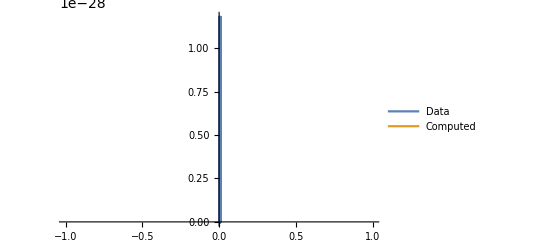

```mathematica
SmoothHistogram[{intensity, RandomVariate[dist,Length[intensity]]},PlotLegends-> {"Data","Computed"}]
```